```mathematica
Morig = {{0,I*J,I*ϵ,-I*J,0,0,-I*ϵ,0,0},{I*J,-4*Γ+2*I*(θ-β),I*α,0,-I*J,0,0,-I*ϵ,0},{I*ϵ,I*α,-4*Γ+2*I*(τ-β),0,0,-I*J,0,0,-I*ϵ},{-I*J,0,0,-4*Γ-2*I*(θ-β),I*J,I*ϵ,-I*α,0,0},{0,-I*J,0,I*J,0,I*α,0,-I*α,0},{0,0,-I*J,I*ϵ,I*α,-4*Γ+2*I*(τ-θ),0,0,-I*α},{-I*ϵ,0,0,-I*α,0,0,-4*Γ-2*I*(τ-β),I*J,I*ϵ},{0,-I*ϵ,0,0,-I*α,0,I*J,-4*Γ-2*I*(τ-θ),I*α},{0,0,-I*ϵ,0,0,-I*α,I*ϵ,I*α,0}};
Morig //TableForm
```

0 | ⅈ J | ⅈ ϵ | -ⅈ J | 0 | 0 | -ⅈ ϵ | 0 | 0
ⅈ J | -4 Γ+2 ⅈ (-β+θ) | ⅈ α | 0 | -ⅈ J | 0 | 0 | -ⅈ ϵ | 0
ⅈ ϵ | ⅈ α | -4 Γ+2 ⅈ (-β+τ) | 0 | 0 | -ⅈ J | 0 | 0 | -ⅈ ϵ
-ⅈ J | 0 | 0 | -4 Γ-2 ⅈ (-β+θ) | ⅈ J | ⅈ ϵ | -ⅈ α | 0 | 0
0 | -ⅈ J | 0 | ⅈ J | 0 | ⅈ α | 0 | -ⅈ α | 0
0 | 0 | -ⅈ J | ⅈ ϵ | ⅈ α | -4 Γ+2 ⅈ (-θ+τ) | 0 | 0 | -ⅈ α
-ⅈ ϵ | 0 | 0 | -ⅈ α | 0 | 0 | -4 Γ-2 ⅈ (-β+τ) | ⅈ J | ⅈ ϵ
0 | -ⅈ ϵ | 0 | 0 | -ⅈ α | 0 | ⅈ J | -4 Γ-2 ⅈ (-θ+τ) | ⅈ α
0 | 0 | -ⅈ ϵ | 0 | 0 | -ⅈ α | ⅈ ϵ | ⅈ α | 0

```mathematica
M = Morig /. {Γ->10^(-5), J->0.1, β->ϵ, θ->ϵ, α->ϵ, τ->0.1}
```

{{0,0.+0.1 ⅈ,ⅈ ϵ,0.-0.1 ⅈ,0,0,-ⅈ ϵ,0,0},{0.+0.1 ⅈ,-1/25000,ⅈ ϵ,0,0.-0.1 ⅈ,0,0,-ⅈ ϵ,0},{ⅈ ϵ,ⅈ ϵ,-1/25000+2 ⅈ (0.1-ϵ),0,0,0.-0.1 ⅈ,0,0,-ⅈ ϵ},{0.-0.1 ⅈ,0,0,-1/25000,0.+0.1 ⅈ,ⅈ ϵ,-ⅈ ϵ,0,0},{0,0.-0.1 ⅈ,0,0.+0.1 ⅈ,0,ⅈ ϵ,0,-ⅈ ϵ,0},{0,0,0.-0.1 ⅈ,ⅈ ϵ,ⅈ ϵ,-1/25000+2 ⅈ (0.1-ϵ),0,0,-ⅈ ϵ},{-ⅈ ϵ,0,0,-ⅈ ϵ,0,0,-1/25000-2 ⅈ (0.1-ϵ),0.+0.1 ⅈ,ⅈ ϵ},{0,-ⅈ ϵ,0,0,-ⅈ ϵ,0,0.+0.1 ⅈ,-1/25000-2 ⅈ (0.1-ϵ),ⅈ ϵ},{0,0,-ⅈ ϵ,0,0,-ⅈ ϵ,ⅈ ϵ,ⅈ ϵ,0}}

```mathematica
(* =========================================*)(*Parameters*)(* =========================================*)
epsilonStart = 10^(-6);
epsilonStop=0.1;
step=10^(-5);

outfile=FileNameJoin[{NotebookDirectory[],"gamma=1e-5; J=0.1.dat"}];


(* =========================================*)
(*Generate epsilon values*)
(* =========================================*)

epsList=Range[epsilonStart,epsilonStop,step];

(*Number of eigenvalues*)
nEvals=Length[Eigenvalues[M/. ϵ->First[epsList]]];

(* =========================================*)
(*Build data table*)
(* =========================================*)
data=Table[Module[{ev},ev= Sort[N[Eigenvalues[N[M /. ϵ -> eps]]]];
Join[{N[eps]},Flatten[{Re[#], Im[#]}&/@ev]]],{eps,epsList}];



(* =========================================*)
(*Export*)
(* =========================================*)

Export[outfile,data,"Table"];

Print["Saved ",Length[data]," rows to ",outfile];
```

Saved 10000 rows to /cptg/u4/kratzel/Documents/Wolfram Mathematica/[3.3] [three-site (degenerate), two-body, general epsilon's, local dephasing, with sigma-z interactions] [june 15]/gamma=1e-5; J=0.1.dat

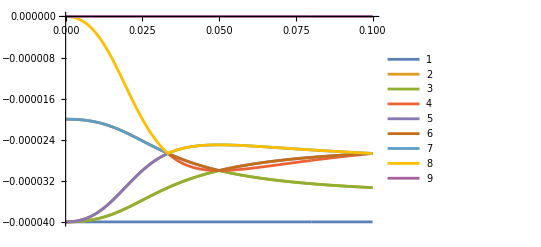

```mathematica
ListLinePlot[data[[All,{1,#}]]&/@Range[2,Length[data[[1]]],2],PlotLegends->Automatic]
```